```mathematica
(*Task 1. SIR*)
Clear["Global`*"]
Nt=10^7;
nio=100;
T=365*3;
syst = {
s'[t]==-beta*s[t]*i[t]-v*(1-1/(1+E^(t-T/3)))*s[t],
i'[t]==beta*s[t]*i[t]-mu*i[t]-d*i[t],
r'[t]==mu*i[t],
r[0]==0,
i[0]==i0,
s[0]==Nt-r[0]-i[0]
};
params={beta, mu, i0,d,v};
ssol=ParametricNDSolveValue[syst, {s[t],i[t],r[t]}, {t,0,T},params]
Manipulate[Plot[{
ssol[beta, mu,i0,d,v][[1]],
ssol[beta, mu,i0,d,v][[2]],
ssol[beta, mu,i0,d,v][[3]]},
{t,0,T},
PlotStyle->{Blue, Red,Orange},
FrameStyle->Directive[Black,15],Frame->True, FrameLabel->{
Style["t",20,Black,FontFamily->"Cambria"],
Style["s[t],i[t],r[t]",20,Black,FontFamily->"Cambria"]},
GridLines->Automatic ,GridLinesStyle->Directive[Gray,Dashed],
PlotRange->Automatic,PlotLegends->Placed[{
Style["s[t]",20,Black,FontFamily->"Cambria"],
Style["i[t]",20,Black,FontFamily->"Cambria"],
Style["r[t]",20,Black,FontFamily->"Cambria"]},Right],ImageSize->612],
{{beta, 1.42*^-8},0,1/Nt}, 
{{mu,0.104},0,0.2}, 
{{d,0.01},0,0.2},
{{v,0},0,0.05},
{{i0,  1}, 0, nio/2}]
```

ParametricFunction[<>]

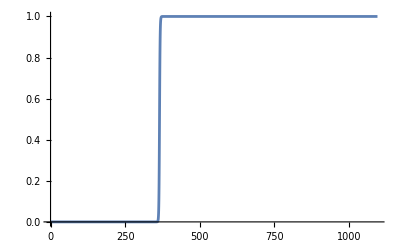

```mathematica
Plot[1-1/(1+E^(t-T/3)),{t,0,T},PlotRange->All]
```